```mathematica
<<NumericalDifferentialEquationAnalysis`
```

```mathematica
IntegrationRule[order_]:=Block[{vecPtosPesos,pts,w,matpsts,xi,eta},
vecPtosPesos=Transpose[GaussianQuadratureWeights[2order,-1,1]];
pts=vecPtosPesos[[1]];
w=vecPtosPesos[[2]];
matpsts=Table[{pts[[j]],pts[[i]],w[[j]] w[[i]] },{i,Length[pts],1,-1},{j,1,Length[pts]}];
matpsts
]
```

```mathematica
ComputeShape[order_,var_]:=Block[{npoints},
npoints=order+1;
tab3[i_,n_]:=Table[If[j==i,1,0],{j,1,n}];
poli3[j_,n_]:=Table[{-1+2 (i-1)/(n-1),tab3[j,n][[i]]},{i,1,n}];
ListPoli[n_]:=Table[InterpolatingPolynomial[poli3[i,n],var],{i,1,n}];
(*list=ListPoli[npoints];
Table[list[[i]],{i,Length[list],1,-1}]*)
ListPoli[npoints]
]
```

```mathematica
GeneratePsis[order_]:=Block[{sz,i,j,w,psis,temp,xi,eta},
sz=(2+order-1)(2+order-1);
psis=Table[0,{sz}];
temp=1;
For[i=1,i≤ 1+order,i++,
For[j=1,j≤ 1+order,j++,
psis[[temp]]=(ComputeShape[order,xi][[j]]ComputeShape[order,eta][[i]])*(1);
temp++;
];
];
psis
];
```

```mathematica
ComputeData[xis_,etas_,Coords_,order_]:=Block[{psis,GradPhi,x,y,Jac,xi,eta},
(*psis=GeneratePsis[order];*)
psis={0.25(1-xi)(1-eta),0.25(1+xi)(1-eta),0.25 (1+xi)(1+eta),0.25(1-xi)(1+eta)};
GradPhi=Table[{D[psis[[i]],xi],D[psis[[i]],eta]},{i,1,Length[psis]}];
x=Sum[psis[[i]]Coords[[i]][[1]],{i,1,Length[psis]}];
y=Sum[psis[[i]]Coords[[i]][[2]],{i,1,Length[psis]}];
Jac={{D[x,xi],D[y,xi]},{D[x,eta],D[y,eta]}};
(*Print["J12 = ",Jac[[1,2]]];*)
{psis,GradPhi,Jac,x,y}/.xi->xis/.eta->etas
]
```

```mathematica
Contribute[data_,weight_,order_]:=Block[{InvJac,GradPsi,nnodes,Jac,GradPhi,DetJ,wpLocal,psi,ek,ef,x,y,i,j},
{psi,GradPsi,Jac,x,y}=data;
(*Print["Jac= ",Jac//MatrixForm];
Print["GradPsi= ",GradPsi//MatrixForm];*)
InvJac=Inverse[Jac];

DetJ=Det[Jac];
(*Print["InvJac= ",InvJac//MatrixForm];*)
(*GradPhi=Table[InvJac .GradPsi[[i]],{i,1,Length[GradPsi]}];*)
(*Print["InvJac =",InvJac];
Print["Transpose[GradPsi] =",Transpose[GradPsi]];*)
GradPhi=InvJac.Transpose[GradPsi];
(*Print[GradPhi];*)
wpLocal=weight  DetJ;
nnodes=4 order;
ek=Table[0,{nnodes},{nnodes}];
ef=Table[0,{nnodes}];
For[i=1,i≤ nnodes,i++,
ef[[i]] +=(Forcing[x,y] psi[[i]])*wpLocal;
For[j=1,j≤ nnodes,j++,
ek[[i,j]]+=(GradPhi[[1,i]]  GradPhi[[1,j]]+GradPhi[[2,i]]  GradPhi[[2,j]])wpLocal;
];
];
Print["ek =",ek//MatrixForm];
{ek,ef}
]
```

```mathematica
Forcing[x_,y_]:=Block[{},
 x x+y y+1
]
```

```mathematica
ContributeElastic[data_,weight_,order_]:=Block[{C,k,B,fu,InvJac,GradPsi,nnodes,Jac,GradPhi,DetJ,wpLocal,psi,ek,ef,x,y,i,j},
nnodes=4 order ;
{psi,GradPsi,Jac,x,y}=data;
(*Print["Jac= ",Jac//MatrixForm];
Print["GradPsi= ",GradPsi//MatrixForm];*)
InvJac=Inverse[Jac];

DetJ=Det[Jac];
(*Print["InvJac= ",InvJac//MatrixForm];*)
(*GradPhi=Table[InvJac .GradPsi[[i]],{i,1,Length[GradPsi]}];*)
(*Print["InvJac =",InvJac];
Print["Transpose[GradPsi] =",Transpose[GradPsi]];*)
GradPhi=InvJac.Transpose[GradPsi];
C=Table[0,{3},{3}];
C[[1,1]]=young/(1-nu^2);
C[[1,2]]=nu young/(1-nu^2);
C[[2,1]]=C[[1,2]];
C[[2,2]]=C[[1,1]];
C[[3,3]]=young/(2 (1+nu));
wpLocal=weight  DetJ;
ek=Table[0,{nnodes 2},{nnodes 2}];
ef=Table[0,{nnodes 2}];
fu=-1;
For[i=1,i≤ nnodes,i++,

(*Print["x = ",x];*)
ef[[2i+fu]] +=(Forcing[x,y] psi[[i]])*wpLocal;
ef[[(2*i+1+fu)]]+=(Forcing[x,y] psi[[i]])*wpLocal;
(*ef[[(2*i+fu)]]+=
ef[[(2*i+fu)]]+=
ef[[(2*i+1+fu)]]+=
ef[[(2*i+1+fu)]]+=*)
For[j=1,j≤ nnodes,j++,
ek[[2 i+fu,2j+fu]]+=( GradPhi[[1,i]] C[[1,1]]  GradPhi[[1,j]]+GradPhi[[2,i]]C[[3,3]]GradPhi[[2,j]])wpLocal ;
ek[[2 i+fu,2j+1+fu]]+=( GradPhi[[1,i]] C[[1,2]]  GradPhi[[2,j]]+GradPhi[[2,i]]C[[3,3]]GradPhi[[1,j]])wpLocal ;
ek[[2 i+1+fu,2j+fu]]+=( GradPhi[[2,i]] C[[1,2]]  GradPhi[[1,j]]+GradPhi[[1,i]]C[[3,3]]GradPhi[[2,j]])wpLocal ;
ek[[2 i+1+fu,2j+1+fu]]+=( GradPhi[[2,i]] C[[2,2]]  GradPhi[[2,j]]+GradPhi[[1,i]]C[[3,3]]GradPhi[[1,j]])wpLocal ;
];
];
(*Print["ek =",ek//MatrixForm];*)
{ek,ef}
]
```

```mathematica
CalcStiff[order_,elcoords_]:=Block[{Dphi,vecPtosPesos,Dpsi,nnodes,Dx,DetJac,psi,InverseJac,InverseDx,gradphixy,wlocal,x,i,ef,ek,j,psis,GradPhi,J,DetJ,InvJ,wpLocal,laplacianContribute,L2Contribute,Ex,F,y,f,xi,eta,w,intrule,intpts,l,h,Jac,data},

intrule=IntegrationRule[order];
intpts=Length[intrule];

nnodes=4 order ;
ek=Table[0,{nnodes },{nnodes }];
ef=Table[0,{nnodes }];

(*Print["intrule =",intrule];
Print["intpts =",intpts];*)
For[l=1,l≤intpts,l++,
For[h=1,h≤ intpts,h++,
xi=intrule[[l,h,1]];
eta=intrule[[l,h,2]];
w=intrule[[l,h,3]];
Print["xi = ",xi];
Print["eta = ",eta];
data=ComputeData[xi,eta,elcoords,order];
{ek,ef}+=Contribute[data,w,order];

];
];
{ek,ef}
]
```

```mathematica
CalcStiffElastic[order_,elcoords_]:=Block[{Dphi,vecPtosPesos,Dpsi,nnodes,Dx,DetJac,psi,InverseJac,InverseDx,gradphixy,wlocal,x,i,ef,ek,j,psis,GradPhi,J,DetJ,InvJ,wpLocal,laplacianContribute,L2Contribute,Ex,F,y,f,xi,eta,w,intrule,intpts,l,h,Jac,data},

intrule=IntegrationRule[order];
intpts=Length[intrule];

nnodes=4 order ;
ek=Table[0,{nnodes 2},{nnodes 2}];
ef=Table[0,{nnodes 2}];

(*Print["intrule =",intrule];
Print["intpts =",intpts];*)
For[l=1,l≤intpts,l++,
For[h=1,h≤ intpts,h++,
xi=intrule[[l,h,1]];
eta=intrule[[l,h,2]];
w=intrule[[l,h,3]];
(*Print["xi = ",xi];
Print["eta = ",eta];*)
data=ComputeData[xi,eta,elcoords,order];
{ek,ef}+=ContributeElastic[data,w,order];

];
];
{ek,ef}
]
```

```mathematica
nodes[order_,coords_]:=Block[{matnode,w,xa,xb,newcoords,i,line1,line2,line3,line4,ya,yb,newtopol,x,y,nodes={},n,j,temp},
If[order==1,Return[coords]];
n=1;
xa=coords[[1,1]];
xb=coords[[2,1]];
y=coords[[1,2]];
line1=Table[{xa+(1-i)(xa-xb)/order,y},{i,1,order+n}];
ya=coords[[2,2]];
yb=coords[[3,2]];
x=coords[[2,1]];
line2=Table[{x,ya+(1-i)(ya-yb)/order},{i,1,order+n}];
xa=coords[[4,1]];
xb=coords[[3,1]];
y=coords[[3,2]];
line3=Table[{xa+(1-i)(xa-xb)/order,y},{i,1,order+n}];
ya=coords[[4,2]];
yb=coords[[1,2]];
x=coords[[1,1]];
line4=Table[{x,ya+(1-i)(ya-yb)/order},{i,1,order+n}];
(*Print[{line1,line2,line3,line4}];*)
Table[AppendTo[nodes,line1[[i]]],{i,1,Length[line1]}];
(*Print["1 = ",nodes];*)
Table[AppendTo[nodes,line2[[i]]],{i,1,Length[line2]}];
(*Print["2 = ",nodes];*)
Table[AppendTo[nodes,line3[[i]]],{i,1,Length[line3]}];
(*Print[ "3 = ",nodes];*)
Table[AppendTo[nodes,line4[[i]]],{i,1,Length[line4]}];
(*Print["4 = ",nodes];*)
For[i=1,i≤ Length[nodes],i++,
temp=nodes[[i]];
For[j=i+1,j≤ Length[nodes],j++,
If[temp==nodes[[j]],
nodes=Delete[nodes,j];

];
];
];
(*{line1,line2,line3,line4}*)
nodes
]
```

```mathematica
Assemble[coords_,nels_,order_,forcing_]:=Block[{i,j,sz,Kglob,k,rows,cols,el,colglob,rowglob,Fglob,Ke,Fe,ik,co},
sz=nels*order+1;
rows=order+1;
cols=rows;
Kglob=Table[0,{sz},{sz}];
Fglob=Table[0,{sz}];
rowglob=1;
colglob=1;

For[k=1,k≤nels,k++,
co=nodes[order,{coords[[k]],coords[[k+1]]}];
{Ke,Fe}=CalcStiffElastic[order,co];
ik=(k-1)*order;
For[i=1,i≤rows,i++,
For[j=1,j≤cols,j++,
Kglob[[ik+i,ik+j]]+=Ke[[i,j]];
];
Fglob[[ik+i]]+=Fe[[i]];
];
];
{Kglob,Fglob}
]
```

```mathematica
ApplyBC[Kglob_,FGlob_,BCcond_]:=Block[{KG=Kglob,FG=FGlob,type1,val1,type2,val2,sz,BIGNUMBER=10^12},

sz=Length[KG];
{type1,val1,type2,val2}=BCcond;



If[type1==1,
(*Dirichlet - Specified Solution *)
KG[[1,1]]=BIGNUMBER;
FG[[1]]=val1 BIGNUMBER;
,
If[type1==2,
(*Newman - Specified Load*)
FG[[1]]+=val1;
,
(*Mixed - Specified Load*)
FG[[1]]+=val1[[2]];
KG[[1,1]]+=val1[[1]];
];

];
If[type2==1,
(*Dirichlet - Specified Solution *)
KG[[sz,sz]]=BIGNUMBER;
FG[[sz]]=val2 BIGNUMBER;
,
If[type2==2,
(*Newman - Specified Load*)
FG[[sz]]+=val2;
,
(*Mixed - Specified Load*)
FG[[sz]]+=val2[[2]];
KG[[sz,sz]]+=val2[[1]];
];

];

{KG,FG}
]
```

```mathematica
coords={{0,0},{10,0},{10,6},{0,6}}
bc={{2,{6000,0}},{3,{6000,0}}}
order=1;
young=10 10^6;
nu=0.3;
mu=young/(2(1+nu));
lambda=young nu/((1+nu)(1-2nu))
{ek,ef}=CalcStiffElastic[order,coords];
Print["Ke = ",ek//MatrixForm];
Print["Fe = ",ef//MatrixForm];
```

{{0,0},{10,0},{10,6},{0,6}}

{{2,{6000,0}},{3,{6000,0}}}

5.76923×10^6

Ke = (4.33455×10^6 | 1.78571×10^6 | -1.12943×10^6 | -137363. | -2.16728×10^6 | -1.78571×10^6 | -1.03785×10^6 | 137363.
1.78571×10^6 | 6.87424×10^6 | 137363. | 2.28327×10^6 | -1.78571×10^6 | -3.43712×10^6 | -137363. | -5.72039×10^6
-1.12943×10^6 | 137363. | 4.33455×10^6 | -1.78571×10^6 | -1.03785×10^6 | -137363. | -2.16728×10^6 | 1.78571×10^6
-137363. | 2.28327×10^6 | -1.78571×10^6 | 6.87424×10^6 | 137363. | -5.72039×10^6 | 1.78571×10^6 | -3.43712×10^6
-2.16728×10^6 | -1.78571×10^6 | -1.03785×10^6 | 137363. | 4.33455×10^6 | 1.78571×10^6 | -1.12943×10^6 | -137363.
-1.78571×10^6 | -3.43712×10^6 | -137363. | -5.72039×10^6 | 1.78571×10^6 | 6.87424×10^6 | 137363. | 2.28327×10^6
-1.03785×10^6 | -137363. | -2.16728×10^6 | 1.78571×10^6 | -1.12943×10^6 | 137363. | 4.33455×10^6 | -1.78571×10^6
137363. | -5.72039×10^6 | 1.78571×10^6 | -3.43712×10^6 | -137363. | 2.28327×10^6 | -1.78571×10^6 | 6.87424×10^6)

Fe = (355.
355.
855.
855.
1035.
1035.
535.
535.)

```mathematica
k//MatrixForm
```

k

```mathematica
ek//MatrixForm
```

(4.33455×10^6 | 1.78571×10^6 | -1.12943×10^6 | -137363. | -2.16728×10^6 | -1.78571×10^6 | -1.03785×10^6 | 137363.
1.78571×10^6 | 6.87424×10^6 | 137363. | 2.28327×10^6 | -1.78571×10^6 | -3.43712×10^6 | -137363. | -5.72039×10^6
-1.12943×10^6 | 137363. | 4.33455×10^6 | -1.78571×10^6 | -1.03785×10^6 | -137363. | -2.16728×10^6 | 1.78571×10^6
-137363. | 2.28327×10^6 | -1.78571×10^6 | 6.87424×10^6 | 137363. | -5.72039×10^6 | 1.78571×10^6 | -3.43712×10^6
-2.16728×10^6 | -1.78571×10^6 | -1.03785×10^6 | 137363. | 4.33455×10^6 | 1.78571×10^6 | -1.12943×10^6 | -137363.
-1.78571×10^6 | -3.43712×10^6 | -137363. | -5.72039×10^6 | 1.78571×10^6 | 6.87424×10^6 | 137363. | 2.28327×10^6
-1.03785×10^6 | -137363. | -2.16728×10^6 | 1.78571×10^6 | -1.12943×10^6 | 137363. | 4.33455×10^6 | -1.78571×10^6
137363. | -5.72039×10^6 | 1.78571×10^6 | -3.43712×10^6 | -137363. | 2.28327×10^6 | -1.78571×10^6 | 6.87424×10^6)

```mathematica
B={{dN1dx,0,dN2dx,0,dN3dx,0,dN4dx,0},{0,dN1dy,0,dN2dy,0,dN3dy,0,dN4dy},{dN1dy,dN1dx,dN2dy,dN2dx,dN3dy,dN3dx,dN4dy,dN4dx}}/.{dN1dx->-(b-y)/(a b),dN2dx->(b-y)/(a b),dN3dx->y/(a b),dN4dx->-y/(a b),dN1dy->-(a-x)/(a b),dN2dy->-x/(a b),dN3dy->x/(a b),dN4dy->(a-x)/(a b)};
c={{EE /(1-Nu^2),EE Nu/(1-Nu^2),0},{EE Nu/(1-Nu^2),EE /(1-Nu^2),0},{0,0,EE/(2(1+Nu))}}/.{EE->young,Nu->nu};
(*c={{C11,C12,0},{C12,C22,0},{0,0,C33}}*)
k=NIntegrate[Transpose[B].c.B/.{a->10,b->6},{x,0,10},{y,0,6}];
Chop[ek-k,10^-5]
```

{{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}}

```mathematica
ii=2;
jj=2;
{2 i+fu,2j+fu}/.{i->ii,j->jj,fu->-1}
{2 i+fu,2j+1+fu}/.{i->ii,j->jj,fu->-1}
{2 i+1+fu,2j+fu}/.{i->ii,j->jj,fu->-1}
{2 i+1+fu,2j+1+fu}/.{i->ii,j->jj,fu->-1}
```

{3,3}

{3,4}

{4,3}

{4,4}

```mathematica
coords={{0,0},{5,0},{5,3},{0,3}}
bc={{2,{6000,0}},{3,{6000,0}}}
order=1;
young=10 10^6;
nu=0.3;
mu=young/(2(1+nu));
lambda=young nu/((1+nu)(1-2nu))
{ek,ef}=CalcStiffElastic[order,coords];
Print["Ke = ",ek//MatrixForm];
Print["Fe = ",ef//MatrixForm];
```

{{0,0},{5,0},{5,3},{0,3}}

{{2,{6000,0}},{3,{6000,0}}}

5.76923×10^6

Ke = (4.33455×10^6 | 1.78571×10^6 | -1.12943×10^6 | -137363. | -2.16728×10^6 | -1.78571×10^6 | -1.03785×10^6 | 137363.
1.78571×10^6 | 6.87424×10^6 | 137363. | 2.28327×10^6 | -1.78571×10^6 | -3.43712×10^6 | -137363. | -5.72039×10^6
-1.12943×10^6 | 137363. | 4.33455×10^6 | -1.78571×10^6 | -1.03785×10^6 | -137363. | -2.16728×10^6 | 1.78571×10^6
-137363. | 2.28327×10^6 | -1.78571×10^6 | 6.87424×10^6 | 137363. | -5.72039×10^6 | 1.78571×10^6 | -3.43712×10^6
-2.16728×10^6 | -1.78571×10^6 | -1.03785×10^6 | 137363. | 4.33455×10^6 | 1.78571×10^6 | -1.12943×10^6 | -137363.
-1.78571×10^6 | -3.43712×10^6 | -137363. | -5.72039×10^6 | 1.78571×10^6 | 6.87424×10^6 | 137363. | 2.28327×10^6
-1.03785×10^6 | -137363. | -2.16728×10^6 | 1.78571×10^6 | -1.12943×10^6 | 137363. | 4.33455×10^6 | -1.78571×10^6
137363. | -5.72039×10^6 | 1.78571×10^6 | -3.43712×10^6 | -137363. | 2.28327×10^6 | -1.78571×10^6 | 6.87424×10^6)

Fe = (25.
25.
56.25
56.25
67.5
67.5
36.25
36.25)

```mathematica
CreateRectangularMesh[a_,b_,nx_,ny_]:=Block[{cols,rows,coords,i,j,deltax,deltay,co1,co2,co3,co4,elvec},

cols=(nx+2);
rows=(ny+2);
coords=Table[0,{rows},{cols}];

deltax=(b[[1]]-a[[1]])/(nx+1);
deltay=(b[[2]]-a[[2]])/(ny+1);
xstart=a[[1]];
ystart=a[[2]];
temp={0,0};

For[i=1,i≤ rows,i++,
For[j=1,j≤cols,j++,
coords[[i,j]]={xstart,ystart};
xstart+=deltax;
];
ystart+=deltay;
xstart=a[[1]];
];

elvec={};
For[i=1,i<rows,i++,
For[j=1,j<cols,j++,
co1=coords[[i,j]];
co2=coords[[i,j+1]];
co3=coords[[i+1,j]];
co4=coords[[i+1,j+1]];
AppendTo[elvec,{co1,co2,co4,co3}];
];
];
elvec
]
```

2

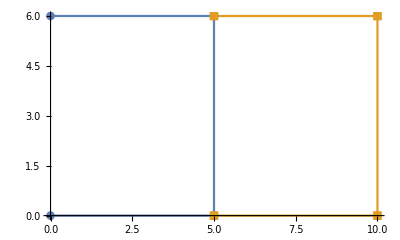

```mathematica
s=CreateRectangularMesh[{0,0},{10,6},1,0];
Length[s]
ListLinePlot[s,AspectRatio->Automatic,PlotMarkers->Automatic,Joined->True]
```

```mathematica
ComputeNNodes[RectangularMesh_]:=Block[{allnodes,i,j,alreadcomputednodes,node,newnode,nnodes,y0,nn,firstrow,resto},
allnodes=Flatten[RectangularMesh,1];
y0=allnodes[[1,2]];
Print[allnodes];
alreadcomputednodes={};
For[i=1,i≤Length[allnodes],i++,
node=allnodes[[i]];
For[j=1+i,j<=Length[allnodes],j++,
If[node==allnodes[[j]], AppendTo[alreadcomputednodes,node]];
];
];
Print[alreadcomputednodes];
newnode=allnodes;
For[i=1,i<=Length[alreadcomputednodes],i++,
newnode=DeleteCases[newnode,alreadcomputednodes[[i]]];
AppendTo[newnode,alreadcomputednodes[[i]]];

];
nn=newnode;
n=nn;
firstrow={};
resto={};
For[i=1,i≤Length[nn],i++,
If[n[[i,2]]==y0,
AppendTo[firstrow,nn[[i]]];
,
AppendTo[resto,nn[[i]]];
];
firstrow=SortBy[firstrow,Last];
resto=SortBy[resto,Last];
resto=Sort[resto,#1[[2]]<#2[[2]]&];
];
PrependTo[resto,firstrow];
ArrayReshape[resto,{Length[nn],2}]
];
```

```mathematica
s//N
```

{{{0.,0.},{5.,0.},{5.,6.},{0.,6.}},{{5.,0.},{10.,0.},{10.,6.},{5.,6.}}}

```mathematica
s[[1,2]]
```

{5,0}

```mathematica
Length[s]
```

2

```mathematica
ComputeNNodes[s]//N
```

{{0,0},{5,0},{5,6},{0,6},{5,0},{10,0},{10,6},{5,6}}

{{5,0},{5,6}}

{{0.,0.},{5.,0.},{10.,0.},{10.,6.},{5.,6.},{0.,6.}}

```mathematica
ComputeTopol[allnodes_]:=Block[{s,ss,i,j,k,topol,topolvec},
topolvec={};
s=allnodes//N;
ss=ComputeNNodes[s]//N;
topolgeral={};
For[i=1,i≤Length[s],i++,

topol=Table[0,{4}];
For[j=1,j≤4,j++,
For[k=1,k≤Length[ss],k++,
If[s[[i,j]]==ss[[k]],
topol[[j]]=k;
AppendTo[topolgeral,k];
];
];

];
AppendTo[topolvec,topol];

];
topolvec
];
```

```mathematica
ComputeTopol[s]
```

{{0.,0.},{5.,0.},{5.,6.},{0.,6.},{5.,0.},{10.,0.},{10.,6.},{5.,6.}}

{{5.,0.},{5.,6.}}

{{1,2,5,6},{2,3,4,5}}

```mathematica
topolgeral
```

{1,2,5,6,2,3,4,5}

```mathematica
topolvec
```

{{1,2,5,6},{2,3,4,5}}

```mathematica
n2=SortBy[n,Last]
Sort[n2,#1[[2]]<#2[[2]]&]
```

{{0,0},{10/3,0},{20/3,0},{10,0},{0,6},{10/3,6},{20/3,6},{10,6}}

{{10,0},{20/3,0},{10/3,0},{0,0},{10,6},{20/3,6},{10/3,6},{0,6}}

```mathematica
a=0;
Ordering[n];
n2=SortBy[n,Last];
Sort[n2,#1[[2]]<#2[[2]]&];
firstrow={};
resto={};
For[i=1,i≤Length[n],i++,
If[n[[i,2]]==a,
AppendTo[firstrow,n[[i]]];
,
AppendTo[resto,n[[i]]];
];
firstrow=SortBy[firstrow,Last];
resto=SortBy[resto,Last];
resto=Sort[resto,#1[[2]]<#2[[2]]&]
]
PrependTo[resto,firstrow]
ArrayReshape[resto,{Length[n],2}]
```

{{{0,0},{10/3,0},{20/3,0},{10,0}},{10,6},{20/3,6},{10/3,6},{0,6}}

{{0,0},{10/3,0},{20/3,0},{10,0},{10,6},{20/3,6},{10/3,6},{0,6}}

```mathematica
firstrow
```

{{0,0},{10,0},{5,0}}

```mathematica
resto
```

{{10,3},{5,3},{0,3},{10,6},{5,6},{0,6}}

```mathematica
firstrow
Flatten[{firstrow},1]
```

{{0,0},{10,0},{5,0}}

{{0,0},{10,0},{5,0}}

```mathematica
newvec=PrependTo[resto,firstrow]
```

{{{0,0},{10,0},{5,0}},{10,3},{5,3},{0,3},{10,6},{5,6},{0,6}}

```mathematica
ArrayReshape[newvec,{Length[newvec],2}]
```

{{0,0},{10,0},{5,0},{10,3},{5,3},{0,3},{10,6}}

```mathematica
Assemble[allcoords_,order_,forcing_]:=Block[{nels,p,i,j,sz,Kglob,k,rows,cols,el,colglob,rowglob,Fglob,Ke,Fe,ik,co,nnodes},

p=order;
nels=Length[allcoords];
nnodes=ComputeNNodes[allcoords];
Print["Nnodes = ",nnodes];
sz=Length[nnodes] 2;
rows=order 8;
cols=rows;
Kglob=Table[0,{sz},{sz}];
Fglob=Table[0,{sz}];
rowglob=1;
colglob=1;
Print["Kglob = ",Kglob//MatrixForm];

For[k=1,k≤nels,k++,
co=nodes[p,allcoords[[k]]];
Print["k = ",k];
Print["co = ",co];
{Ke,Fe}=CalcStiffElastic[order,co];
Print["Ke = ",Ke//MatrixForm];

ik=(k-1)*order 4;
For[i=1,i≤rows,i++,
For[j=1,j≤cols,j++,
Kglob[[ik+i,ik+j]]+=Ke[[i,j]];
];
Fglob[[ik+i]]+=Fe[[i]];
];
Print["Kglob = ",Kglob//MatrixForm]
];
{Kglob,Fglob}
]
```

```mathematica
ComputeTopol[allnodes_]:=Block[{s,ss,i,j,k,topol,topolvec},
topolvec={};
s=allnodes//N;
ss=ComputeNNodes[s]//N;
topolgeral={};
For[i=1,i≤Length[s],i++,

topol=Table[0,{4}];
For[j=1,j≤4,j++,
For[k=1,k≤Length[ss],k++,
If[s[[i,j]]==ss[[k]],
topol[[j]]=k;
AppendTo[topolgeral,k];
];
];

];
AppendTo[topolvec,topol];

];
topolvec
];
```

```mathematica
topolgeral
```

{1,2,3,4}

# -Graphics-

# -Graphics-

```mathematica
Assemble[allcoords_,order_,forcing_]:=Block[{fu,nels,p,i,j,sz,Kglob,k,rows,cols,el,colglob,rowglob,Fglob,Ke,Fe,ik,co,nnodes},

p=order;
nels=Length[allcoords];
nnodes=ComputeNNodes[allcoords];
Print["Nnodes = ",nnodes];
sz=Length[nnodes] 2;
rows=order 4;
cols=rows;
Kglob=Table[0,{sz},{sz}];
Fglob=Table[0,{sz}];
Print["Kglob = ",Kglob//MatrixForm];

(*for(Int i=0;i<NumElements;i++)
{
fMalha->getElement(i)->CalcStiff(*fMalha,Kelem,Felem,i);
const VecInt&elvec=fMalha->getElement(i)->getNodeVec();
for(Int row=0;row<Kelem.nrows();row++)
 {
Int rowglob=elvec[row];
for(Int col=0;col<Kelem.ncols();col++) {
Int colglob=elvec[col];
stiff[rowglob][colglob]+=Kelem[row][col];
} 
rhs[rowglob][0]+=Felem[row][0];
}
}

*)
*)
topol=ComputeTopol[allcoords];
Print["topol = ",topol];
For[k=1,k≤nels,k++,
co=nodes[p,allcoords[[k]]];
Print["k = ",k];
Print["co = ",co];
{Ke,Fe}=CalcStiffElastic[order,co];
Print["Ke = ",Ke//MatrixForm];

ik=(k-1)*order 4;
fu=-1;
For[i=1,i≤rows,i++,
rowglob=topol[[k,i]];
For[j=1,j≤cols,j++,
colglob=topol[[k,j]];
Kglob[[2 rowglob+fu,2 colglob+fu]]+=Ke[[2 i+fu,2 j+fu]];
Kglob[[2rowglob+fu,2colglob+1+fu]]+=Ke[[2i+fu,2j+1+fu]];
Kglob[[2rowglob+1+fu,2colglob+fu]]+=Ke[[2i+1+fu,2j+fu]];
Kglob[[2rowglob+1+fu,2colglob+1+fu]]+=Ke[[2i+1+fu,2j+1+fu]];

];
Fglob[[2rowglob+fu]]+=Fe[[i]];
];
];
{Kglob,Fglob}
]
```

```mathematica
allcoords=CreateRectangularMesh[{0,0},{10,6},1,0];
{KE,FE}=Assemble[allcoords,1,1];
Print["KE = ",KE//MatrixForm]
(*order=1;
nels=Length[allcoords];
p=order;
ekt=0.;
eft=0.;
For[i=1,i≤nels,i++,
nodess=nodes[p,allcoords[[i]]];
Print["el = ",i ];
Print["nodes = ",nodess];
{ek,ef}=CalcStiffElastic[order,nodess];


];

ListPlot[matnode,AspectRatio->Automatic]*)
```

{{0,0},{5,0},{5,6},{0,6},{5,0},{10,0},{10,6},{5,6}}

{{5,0},{5,6}}

Nnodes = {{0,0},{5,0},{10,0},{10,6},{5,6},{0,6}}

Kglob = (0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

{{0.,0.},{5.,0.},{5.,6.},{0.,6.},{5.,0.},{10.,0.},{10.,6.},{5.,6.}}

{{5.,0.},{5.,6.}}

topol = {{1,2,5,6},{2,3,4,5}}

k = 1

co = {{0,0},{5,0},{5,6},{0,6}}

Ke = (5.46398×10^6 | 1.78571×10^6 | -3.86142×10^6 | -137363. | -2.73199×10^6 | -1.78571×10^6 | 1.12943×10^6 | 137363.
1.78571×10^6 | 4.59096×10^6 | 137363. | -12210. | -1.78571×10^6 | -2.29548×10^6 | -137363. | -2.28327×10^6
-3.86142×10^6 | 137363. | 5.46398×10^6 | -1.78571×10^6 | 1.12943×10^6 | -137363. | -2.73199×10^6 | 1.78571×10^6
-137363. | -12210. | -1.78571×10^6 | 4.59096×10^6 | 137363. | -2.28327×10^6 | 1.78571×10^6 | -2.29548×10^6
-2.73199×10^6 | -1.78571×10^6 | 1.12943×10^6 | 137363. | 5.46398×10^6 | 1.78571×10^6 | -3.86142×10^6 | -137363.
-1.78571×10^6 | -2.29548×10^6 | -137363. | -2.28327×10^6 | 1.78571×10^6 | 4.59096×10^6 | 137363. | -12210.
1.12943×10^6 | -137363. | -2.73199×10^6 | 1.78571×10^6 | -3.86142×10^6 | 137363. | 5.46398×10^6 | -1.78571×10^6
137363. | -2.28327×10^6 | 1.78571×10^6 | -2.29548×10^6 | -137363. | -12210. | -1.78571×10^6 | 4.59096×10^6)

k = 2

co = {{5,0},{10,0},{10,6},{5,6}}

Ke = (5.46398×10^6 | 1.78571×10^6 | -3.86142×10^6 | -137363. | -2.73199×10^6 | -1.78571×10^6 | 1.12943×10^6 | 137363.
1.78571×10^6 | 4.59096×10^6 | 137363. | -12210. | -1.78571×10^6 | -2.29548×10^6 | -137363. | -2.28327×10^6
-3.86142×10^6 | 137363. | 5.46398×10^6 | -1.78571×10^6 | 1.12943×10^6 | -137363. | -2.73199×10^6 | 1.78571×10^6
-137363. | -12210. | -1.78571×10^6 | 4.59096×10^6 | 137363. | -2.28327×10^6 | 1.78571×10^6 | -2.29548×10^6
-2.73199×10^6 | -1.78571×10^6 | 1.12943×10^6 | 137363. | 5.46398×10^6 | 1.78571×10^6 | -3.86142×10^6 | -137363.
-1.78571×10^6 | -2.29548×10^6 | -137363. | -2.28327×10^6 | 1.78571×10^6 | 4.59096×10^6 | 137363. | -12210.
1.12943×10^6 | -137363. | -2.73199×10^6 | 1.78571×10^6 | -3.86142×10^6 | 137363. | 5.46398×10^6 | -1.78571×10^6
137363. | -2.28327×10^6 | 1.78571×10^6 | -2.29548×10^6 | -137363. | -12210. | -1.78571×10^6 | 4.59096×10^6)

KE = (5.46398×10^6 | 1.78571×10^6 | -3.86142×10^6 | -137363. | 0 | 0 | 0 | 0 | -2.73199×10^6 | -1.78571×10^6 | 1.12943×10^6 | 137363.
1.78571×10^6 | 4.59096×10^6 | 137363. | -12210. | 0 | 0 | 0 | 0 | -1.78571×10^6 | -2.29548×10^6 | -137363. | -2.28327×10^6
-3.86142×10^6 | 137363. | 1.0928×10^7 | 0. | -3.86142×10^6 | -137363. | -2.73199×10^6 | -1.78571×10^6 | 2.25885×10^6 | 0. | -2.73199×10^6 | 1.78571×10^6
-137363. | -12210. | 0. | 9.18193×10^6 | 137363. | -12210. | -1.78571×10^6 | -2.29548×10^6 | 0. | -4.56654×10^6 | 1.78571×10^6 | -2.29548×10^6
0 | 0 | -3.86142×10^6 | 137363. | 5.46398×10^6 | -1.78571×10^6 | 1.12943×10^6 | -137363. | -2.73199×10^6 | 1.78571×10^6 | 0 | 0
0 | 0 | -137363. | -12210. | -1.78571×10^6 | 4.59096×10^6 | 137363. | -2.28327×10^6 | 1.78571×10^6 | -2.29548×10^6 | 0 | 0
0 | 0 | -2.73199×10^6 | -1.78571×10^6 | 1.12943×10^6 | 137363. | 5.46398×10^6 | 1.78571×10^6 | -3.86142×10^6 | -137363. | 0 | 0
0 | 0 | -1.78571×10^6 | -2.29548×10^6 | -137363. | -2.28327×10^6 | 1.78571×10^6 | 4.59096×10^6 | 137363. | -12210. | 0 | 0
-2.73199×10^6 | -1.78571×10^6 | 2.25885×10^6 | 0. | -2.73199×10^6 | 1.78571×10^6 | -3.86142×10^6 | 137363. | 1.0928×10^7 | -2.32831×10^-10 | -3.86142×10^6 | -137363.
-1.78571×10^6 | -2.29548×10^6 | -2.91038×10^-11 | -4.56654×10^6 | 1.78571×10^6 | -2.29548×10^6 | -137363. | -12210. | -2.32831×10^-10 | 9.18193×10^6 | 137363. | -12210.
1.12943×10^6 | -137363. | -2.73199×10^6 | 1.78571×10^6 | 0 | 0 | 0 | 0 | -3.86142×10^6 | 137363. | 5.46398×10^6 | -1.78571×10^6
137363. | -2.28327×10^6 | 1.78571×10^6 | -2.29548×10^6 | 0 | 0 | 0 | 0 | -137363. | -12210. | -1.78571×10^6 | 4.59096×10^6)

```mathematica
5.463980463980462 10^6 + 5.463980463980463 10^6
```

1.0928×10^7

```mathematica
-1.7857142857142857 10^6 +1.7857142857142857 10^6
```

0.

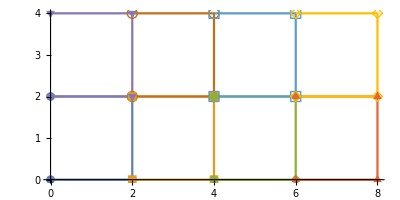

Nnodes = 15

Kglob = (0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

k = 1

co = {{0,0},{2,0},{2,2},{0,2}}

Ke = (4.94505×10^6 | 1.78571×10^6 | -3.02198×10^6 | -137363. | -2.47253×10^6 | -1.78571×10^6 | 549451. | 137363.
1.78571×10^6 | 4.94505×10^6 | 137363. | 549451. | -1.78571×10^6 | -2.47253×10^6 | -137363. | -3.02198×10^6
-3.02198×10^6 | 137363. | 4.94505×10^6 | -1.78571×10^6 | 549451. | -137363. | -2.47253×10^6 | 1.78571×10^6
-137363. | 549451. | -1.78571×10^6 | 4.94505×10^6 | 137363. | -3.02198×10^6 | 1.78571×10^6 | -2.47253×10^6
-2.47253×10^6 | -1.78571×10^6 | 549451. | 137363. | 4.94505×10^6 | 1.78571×10^6 | -3.02198×10^6 | -137363.
-1.78571×10^6 | -2.47253×10^6 | -137363. | -3.02198×10^6 | 1.78571×10^6 | 4.94505×10^6 | 137363. | 549451.
549451. | -137363. | -2.47253×10^6 | 1.78571×10^6 | -3.02198×10^6 | 137363. | 4.94505×10^6 | -1.78571×10^6
137363. | -3.02198×10^6 | 1.78571×10^6 | -2.47253×10^6 | -137363. | 549451. | -1.78571×10^6 | 4.94505×10^6)

Kglob = (4.94505×10^6 | 1.78571×10^6 | -3.02198×10^6 | -137363. | -2.47253×10^6 | -1.78571×10^6 | 549451. | 137363. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1.78571×10^6 | 4.94505×10^6 | 137363. | 549451. | -1.78571×10^6 | -2.47253×10^6 | -137363. | -3.02198×10^6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-3.02198×10^6 | 137363. | 4.94505×10^6 | -1.78571×10^6 | 549451. | -137363. | -2.47253×10^6 | 1.78571×10^6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-137363. | 549451. | -1.78571×10^6 | 4.94505×10^6 | 137363. | -3.02198×10^6 | 1.78571×10^6 | -2.47253×10^6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-2.47253×10^6 | -1.78571×10^6 | 549451. | 137363. | 4.94505×10^6 | 1.78571×10^6 | -3.02198×10^6 | -137363. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1.78571×10^6 | -2.47253×10^6 | -137363. | -3.02198×10^6 | 1.78571×10^6 | 4.94505×10^6 | 137363. | 549451. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
549451. | -137363. | -2.47253×10^6 | 1.78571×10^6 | -3.02198×10^6 | 137363. | 4.94505×10^6 | -1.78571×10^6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
137363. | -3.02198×10^6 | 1.78571×10^6 | -2.47253×10^6 | -137363. | 549451. | -1.78571×10^6 | 4.94505×10^6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

k = 2

co = {{2,0},{4,0},{4,2},{2,2}}

Ke = (4.94505×10^6 | 1.78571×10^6 | -3.02198×10^6 | -137363. | -2.47253×10^6 | -1.78571×10^6 | 549451. | 137363.
1.78571×10^6 | 4.94505×10^6 | 137363. | 549451. | -1.78571×10^6 | -2.47253×10^6 | -137363. | -3.02198×10^6
-3.02198×10^6 | 137363. | 4.94505×10^6 | -1.78571×10^6 | 549451. | -137363. | -2.47253×10^6 | 1.78571×10^6
-137363. | 549451. | -1.78571×10^6 | 4.94505×10^6 | 137363. | -3.02198×10^6 | 1.78571×10^6 | -2.47253×10^6
-2.47253×10^6 | -1.78571×10^6 | 549451. | 137363. | 4.94505×10^6 | 1.78571×10^6 | -3.02198×10^6 | -137363.
-1.78571×10^6 | -2.47253×10^6 | -137363. | -3.02198×10^6 | 1.78571×10^6 | 4.94505×10^6 | 137363. | 549451.
549451. | -137363. | -2.47253×10^6 | 1.78571×10^6 | -3.02198×10^6 | 137363. | 4.94505×10^6 | -1.78571×10^6
137363. | -3.02198×10^6 | 1.78571×10^6 | -2.47253×10^6 | -137363. | 549451. | -1.78571×10^6 | 4.94505×10^6)

Kglob = (4.94505×10^6 | 1.78571×10^6 | -3.02198×10^6 | -137363. | -2.47253×10^6 | -1.78571×10^6 | 549451. | 137363. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1.78571×10^6 | 4.94505×10^6 | 137363. | 549451. | -1.78571×10^6 | -2.47253×10^6 | -137363. | -3.02198×10^6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-3.02198×10^6 | 137363. | 4.94505×10^6 | -1.78571×10^6 | 549451. | -137363. | -2.47253×10^6 | 1.78571×10^6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-137363. | 549451. | -1.78571×10^6 | 4.94505×10^6 | 137363. | -3.02198×10^6 | 1.78571×10^6 | -2.47253×10^6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-2.47253×10^6 | -1.78571×10^6 | 549451. | 137363. | 9.89011×10^6 | 3.57143×10^6 | -6.04396×10^6 | -274725. | -2.47253×10^6 | -1.78571×10^6 | 549451. | 137363. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1.78571×10^6 | -2.47253×10^6 | -137363. | -3.02198×10^6 | 3.57143×10^6 | 9.89011×10^6 | 274725. | 1.0989×10^6 | -1.78571×10^6 | -2.47253×10^6 | -137363. | -3.02198×10^6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
549451. | -137363. | -2.47253×10^6 | 1.78571×10^6 | -6.04396×10^6 | 274725. | 9.89011×10^6 | -3.57143×10^6 | 549451. | -137363. | -2.47253×10^6 | 1.78571×10^6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
137363. | -3.02198×10^6 | 1.78571×10^6 | -2.47253×10^6 | -274725. | 1.0989×10^6 | -3.57143×10^6 | 9.89011×10^6 | 137363. | -3.02198×10^6 | 1.78571×10^6 | -2.47253×10^6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -2.47253×10^6 | -1.78571×10^6 | 549451. | 137363. | 4.94505×10^6 | 1.78571×10^6 | -3.02198×10^6 | -137363. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1.78571×10^6 | -2.47253×10^6 | -137363. | -3.02198×10^6 | 1.78571×10^6 | 4.94505×10^6 | 137363. | 549451. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 549451. | -137363. | -2.47253×10^6 | 1.78571×10^6 | -3.02198×10^6 | 137363. | 4.94505×10^6 | -1.78571×10^6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 137363. | -3.02198×10^6 | 1.78571×10^6 | -2.47253×10^6 | -137363. | 549451. | -1.78571×10^6 | 4.94505×10^6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

k = 3

co = {{4,0},{6,0},{6,2},{4,2}}

Ke = (4.94505×10^6 | 1.78571×10^6 | -3.02198×10^6 | -137363. | -2.47253×10^6 | -1.78571×10^6 | 549451. | 137363.
1.78571×10^6 | 4.94505×10^6 | 137363. | 549451. | -1.78571×10^6 | -2.47253×10^6 | -137363. | -3.02198×10^6
-3.02198×10^6 | 137363. | 4.94505×10^6 | -1.78571×10^6 | 549451. | -137363. | -2.47253×10^6 | 1.78571×10^6
-137363. | 549451. | -1.78571×10^6 | 4.94505×10^6 | 137363. | -3.02198×10^6 | 1.78571×10^6 | -2.47253×10^6
-2.47253×10^6 | -1.78571×10^6 | 549451. | 137363. | 4.94505×10^6 | 1.78571×10^6 | -3.02198×10^6 | -137363.
-1.78571×10^6 | -2.47253×10^6 | -137363. | -3.02198×10^6 | 1.78571×10^6 | 4.94505×10^6 | 137363. | 549451.
549451. | -137363. | -2.47253×10^6 | 1.78571×10^6 | -3.02198×10^6 | 137363. | 4.94505×10^6 | -1.78571×10^6
137363. | -3.02198×10^6 | 1.78571×10^6 | -2.47253×10^6 | -137363. | 549451. | -1.78571×10^6 | 4.94505×10^6)

Kglob = (4.94505×10^6 | 1.78571×10^6 | -3.02198×10^6 | -137363. | -2.47253×10^6 | -1.78571×10^6 | 549451. | 137363. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1.78571×10^6 | 4.94505×10^6 | 137363. | 549451. | -1.78571×10^6 | -2.47253×10^6 | -137363. | -3.02198×10^6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-3.02198×10^6 | 137363. | 4.94505×10^6 | -1.78571×10^6 | 549451. | -137363. | -2.47253×10^6 | 1.78571×10^6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-137363. | 549451. | -1.78571×10^6 | 4.94505×10^6 | 137363. | -3.02198×10^6 | 1.78571×10^6 | -2.47253×10^6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-2.47253×10^6 | -1.78571×10^6 | 549451. | 137363. | 9.89011×10^6 | 3.57143×10^6 | -6.04396×10^6 | -274725. | -2.47253×10^6 | -1.78571×10^6 | 549451. | 137363. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1.78571×10^6 | -2.47253×10^6 | -137363. | -3.02198×10^6 | 3.57143×10^6 | 9.89011×10^6 | 274725. | 1.0989×10^6 | -1.78571×10^6 | -2.47253×10^6 | -137363. | -3.02198×10^6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
549451. | -137363. | -2.47253×10^6 | 1.78571×10^6 | -6.04396×10^6 | 274725. | 9.89011×10^6 | -3.57143×10^6 | 549451. | -137363. | -2.47253×10^6 | 1.78571×10^6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
137363. | -3.02198×10^6 | 1.78571×10^6 | -2.47253×10^6 | -274725. | 1.0989×10^6 | -3.57143×10^6 | 9.89011×10^6 | 137363. | -3.02198×10^6 | 1.78571×10^6 | -2.47253×10^6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -2.47253×10^6 | -1.78571×10^6 | 549451. | 137363. | 9.89011×10^6 | 3.57143×10^6 | -6.04396×10^6 | -274725. | -2.47253×10^6 | -1.78571×10^6 | 549451. | 137363. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1.78571×10^6 | -2.47253×10^6 | -137363. | -3.02198×10^6 | 3.57143×10^6 | 9.89011×10^6 | 274725. | 1.0989×10^6 | -1.78571×10^6 | -2.47253×10^6 | -137363. | -3.02198×10^6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 549451. | -137363. | -2.47253×10^6 | 1.78571×10^6 | -6.04396×10^6 | 274725. | 9.89011×10^6 | -3.57143×10^6 | 549451. | -137363. | -2.47253×10^6 | 1.78571×10^6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 137363. | -3.02198×10^6 | 1.78571×10^6 | -2.47253×10^6 | -274725. | 1.0989×10^6 | -3.57143×10^6 | 9.89011×10^6 | 137363. | -3.02198×10^6 | 1.78571×10^6 | -2.47253×10^6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2.47253×10^6 | -1.78571×10^6 | 549451. | 137363. | 4.94505×10^6 | 1.78571×10^6 | -3.02198×10^6 | -137363. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1.78571×10^6 | -2.47253×10^6 | -137363. | -3.02198×10^6 | 1.78571×10^6 | 4.94505×10^6 | 137363. | 549451. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 549451. | -137363. | -2.47253×10^6 | 1.78571×10^6 | -3.02198×10^6 | 137363. | 4.94505×10^6 | -1.78571×10^6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 137363. | -3.02198×10^6 | 1.78571×10^6 | -2.47253×10^6 | -137363. | 549451. | -1.78571×10^6 | 4.94505×10^6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

k = 4

co = {{6,0},{8,0},{8,2},{6,2}}

Ke = (4.94505×10^6 | 1.78571×10^6 | -3.02198×10^6 | -137363. | -2.47253×10^6 | -1.78571×10^6 | 549451. | 137363.
1.78571×10^6 | 4.94505×10^6 | 137363. | 549451. | -1.78571×10^6 | -2.47253×10^6 | -137363. | -3.02198×10^6
-3.02198×10^6 | 137363. | 4.94505×10^6 | -1.78571×10^6 | 549451. | -137363. | -2.47253×10^6 | 1.78571×10^6
-137363. | 549451. | -1.78571×10^6 | 4.94505×10^6 | 137363. | -3.02198×10^6 | 1.78571×10^6 | -2.47253×10^6
-2.47253×10^6 | -1.78571×10^6 | 549451. | 137363. | 4.94505×10^6 | 1.78571×10^6 | -3.02198×10^6 | -137363.
-1.78571×10^6 | -2.47253×10^6 | -137363. | -3.02198×10^6 | 1.78571×10^6 | 4.94505×10^6 | 137363. | 549451.
549451. | -137363. | -2.47253×10^6 | 1.78571×10^6 | -3.02198×10^6 | 137363. | 4.94505×10^6 | -1.78571×10^6
137363. | -3.02198×10^6 | 1.78571×10^6 | -2.47253×10^6 | -137363. | 549451. | -1.78571×10^6 | 4.94505×10^6)

Kglob = (4.94505×10^6 | 1.78571×10^6 | -3.02198×10^6 | -137363. | -2.47253×10^6 | -1.78571×10^6 | 549451. | 137363. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1.78571×10^6 | 4.94505×10^6 | 137363. | 549451. | -1.78571×10^6 | -2.47253×10^6 | -137363. | -3.02198×10^6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-3.02198×10^6 | 137363. | 4.94505×10^6 | -1.78571×10^6 | 549451. | -137363. | -2.47253×10^6 | 1.78571×10^6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-137363. | 549451. | -1.78571×10^6 | 4.94505×10^6 | 137363. | -3.02198×10^6 | 1.78571×10^6 | -2.47253×10^6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-2.47253×10^6 | -1.78571×10^6 | 549451. | 137363. | 9.89011×10^6 | 3.57143×10^6 | -6.04396×10^6 | -274725. | -2.47253×10^6 | -1.78571×10^6 | 549451. | 137363. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1.78571×10^6 | -2.47253×10^6 | -137363. | -3.02198×10^6 | 3.57143×10^6 | 9.89011×10^6 | 274725. | 1.0989×10^6 | -1.78571×10^6 | -2.47253×10^6 | -137363. | -3.02198×10^6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
549451. | -137363. | -2.47253×10^6 | 1.78571×10^6 | -6.04396×10^6 | 274725. | 9.89011×10^6 | -3.57143×10^6 | 549451. | -137363. | -2.47253×10^6 | 1.78571×10^6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
137363. | -3.02198×10^6 | 1.78571×10^6 | -2.47253×10^6 | -274725. | 1.0989×10^6 | -3.57143×10^6 | 9.89011×10^6 | 137363. | -3.02198×10^6 | 1.78571×10^6 | -2.47253×10^6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -2.47253×10^6 | -1.78571×10^6 | 549451. | 137363. | 9.89011×10^6 | 3.57143×10^6 | -6.04396×10^6 | -274725. | -2.47253×10^6 | -1.78571×10^6 | 549451. | 137363. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1.78571×10^6 | -2.47253×10^6 | -137363. | -3.02198×10^6 | 3.57143×10^6 | 9.89011×10^6 | 274725. | 1.0989×10^6 | -1.78571×10^6 | -2.47253×10^6 | -137363. | -3.02198×10^6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 549451. | -137363. | -2.47253×10^6 | 1.78571×10^6 | -6.04396×10^6 | 274725. | 9.89011×10^6 | -3.57143×10^6 | 549451. | -137363. | -2.47253×10^6 | 1.78571×10^6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 137363. | -3.02198×10^6 | 1.78571×10^6 | -2.47253×10^6 | -274725. | 1.0989×10^6 | -3.57143×10^6 | 9.89011×10^6 | 137363. | -3.02198×10^6 | 1.78571×10^6 | -2.47253×10^6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2.47253×10^6 | -1.78571×10^6 | 549451. | 137363. | 9.89011×10^6 | 3.57143×10^6 | -6.04396×10^6 | -274725. | -2.47253×10^6 | -1.78571×10^6 | 549451. | 137363. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1.78571×10^6 | -2.47253×10^6 | -137363. | -3.02198×10^6 | 3.57143×10^6 | 9.89011×10^6 | 274725. | 1.0989×10^6 | -1.78571×10^6 | -2.47253×10^6 | -137363. | -3.02198×10^6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 549451. | -137363. | -2.47253×10^6 | 1.78571×10^6 | -6.04396×10^6 | 274725. | 9.89011×10^6 | -3.57143×10^6 | 549451. | -137363. | -2.47253×10^6 | 1.78571×10^6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 137363. | -3.02198×10^6 | 1.78571×10^6 | -2.47253×10^6 | -274725. | 1.0989×10^6 | -3.57143×10^6 | 9.89011×10^6 | 137363. | -3.02198×10^6 | 1.78571×10^6 | -2.47253×10^6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2.47253×10^6 | -1.78571×10^6 | 549451. | 137363. | 4.94505×10^6 | 1.78571×10^6 | -3.02198×10^6 | -137363. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1.78571×10^6 | -2.47253×10^6 | -137363. | -3.02198×10^6 | 1.78571×10^6 | 4.94505×10^6 | 137363. | 549451. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 549451. | -137363. | -2.47253×10^6 | 1.78571×10^6 | -3.02198×10^6 | 137363. | 4.94505×10^6 | -1.78571×10^6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 137363. | -3.02198×10^6 | 1.78571×10^6 | -2.47253×10^6 | -137363. | 549451. | -1.78571×10^6 | 4.94505×10^6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

k = 5

co = {{0,2},{2,2},{2,4},{0,4}}

Ke = (4.94505×10^6 | 1.78571×10^6 | -3.02198×10^6 | -137363. | -2.47253×10^6 | -1.78571×10^6 | 549451. | 137363.
1.78571×10^6 | 4.94505×10^6 | 137363. | 549451. | -1.78571×10^6 | -2.47253×10^6 | -137363. | -3.02198×10^6
-3.02198×10^6 | 137363. | 4.94505×10^6 | -1.78571×10^6 | 549451. | -137363. | -2.47253×10^6 | 1.78571×10^6
-137363. | 549451. | -1.78571×10^6 | 4.94505×10^6 | 137363. | -3.02198×10^6 | 1.78571×10^6 | -2.47253×10^6
-2.47253×10^6 | -1.78571×10^6 | 549451. | 137363. | 4.94505×10^6 | 1.78571×10^6 | -3.02198×10^6 | -137363.
-1.78571×10^6 | -2.47253×10^6 | -137363. | -3.02198×10^6 | 1.78571×10^6 | 4.94505×10^6 | 137363. | 549451.
549451. | -137363. | -2.47253×10^6 | 1.78571×10^6 | -3.02198×10^6 | 137363. | 4.94505×10^6 | -1.78571×10^6
137363. | -3.02198×10^6 | 1.78571×10^6 | -2.47253×10^6 | -137363. | 549451. | -1.78571×10^6 | 4.94505×10^6)

Kglob = (4.94505×10^6 | 1.78571×10^6 | -3.02198×10^6 | -137363. | -2.47253×10^6 | -1.78571×10^6 | 549451. | 137363. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1.78571×10^6 | 4.94505×10^6 | 137363. | 549451. | -1.78571×10^6 | -2.47253×10^6 | -137363. | -3.02198×10^6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-3.02198×10^6 | 137363. | 4.94505×10^6 | -1.78571×10^6 | 549451. | -137363. | -2.47253×10^6 | 1.78571×10^6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-137363. | 549451. | -1.78571×10^6 | 4.94505×10^6 | 137363. | -3.02198×10^6 | 1.78571×10^6 | -2.47253×10^6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-2.47253×10^6 | -1.78571×10^6 | 549451. | 137363. | 9.89011×10^6 | 3.57143×10^6 | -6.04396×10^6 | -274725. | -2.47253×10^6 | -1.78571×10^6 | 549451. | 137363. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1.78571×10^6 | -2.47253×10^6 | -137363. | -3.02198×10^6 | 3.57143×10^6 | 9.89011×10^6 | 274725. | 1.0989×10^6 | -1.78571×10^6 | -2.47253×10^6 | -137363. | -3.02198×10^6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
549451. | -137363. | -2.47253×10^6 | 1.78571×10^6 | -6.04396×10^6 | 274725. | 9.89011×10^6 | -3.57143×10^6 | 549451. | -137363. | -2.47253×10^6 | 1.78571×10^6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
137363. | -3.02198×10^6 | 1.78571×10^6 | -2.47253×10^6 | -274725. | 1.0989×10^6 | -3.57143×10^6 | 9.89011×10^6 | 137363. | -3.02198×10^6 | 1.78571×10^6 | -2.47253×10^6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -2.47253×10^6 | -1.78571×10^6 | 549451. | 137363. | 9.89011×10^6 | 3.57143×10^6 | -6.04396×10^6 | -274725. | -2.47253×10^6 | -1.78571×10^6 | 549451. | 137363. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1.78571×10^6 | -2.47253×10^6 | -137363. | -3.02198×10^6 | 3.57143×10^6 | 9.89011×10^6 | 274725. | 1.0989×10^6 | -1.78571×10^6 | -2.47253×10^6 | -137363. | -3.02198×10^6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 549451. | -137363. | -2.47253×10^6 | 1.78571×10^6 | -6.04396×10^6 | 274725. | 9.89011×10^6 | -3.57143×10^6 | 549451. | -137363. | -2.47253×10^6 | 1.78571×10^6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 137363. | -3.02198×10^6 | 1.78571×10^6 | -2.47253×10^6 | -274725. | 1.0989×10^6 | -3.57143×10^6 | 9.89011×10^6 | 137363. | -3.02198×10^6 | 1.78571×10^6 | -2.47253×10^6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2.47253×10^6 | -1.78571×10^6 | 549451. | 137363. | 9.89011×10^6 | 3.57143×10^6 | -6.04396×10^6 | -274725. | -2.47253×10^6 | -1.78571×10^6 | 549451. | 137363. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1.78571×10^6 | -2.47253×10^6 | -137363. | -3.02198×10^6 | 3.57143×10^6 | 9.89011×10^6 | 274725. | 1.0989×10^6 | -1.78571×10^6 | -2.47253×10^6 | -137363. | -3.02198×10^6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 549451. | -137363. | -2.47253×10^6 | 1.78571×10^6 | -6.04396×10^6 | 274725. | 9.89011×10^6 | -3.57143×10^6 | 549451. | -137363. | -2.47253×10^6 | 1.78571×10^6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 137363. | -3.02198×10^6 | 1.78571×10^6 | -2.47253×10^6 | -274725. | 1.0989×10^6 | -3.57143×10^6 | 9.89011×10^6 | 137363. | -3.02198×10^6 | 1.78571×10^6 | -2.47253×10^6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2.47253×10^6 | -1.78571×10^6 | 549451. | 137363. | 9.89011×10^6 | 3.57143×10^6 | -6.04396×10^6 | -274725. | -2.47253×10^6 | -1.78571×10^6 | 549451. | 137363. | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1.78571×10^6 | -2.47253×10^6 | -137363. | -3.02198×10^6 | 3.57143×10^6 | 9.89011×10^6 | 274725. | 1.0989×10^6 | -1.78571×10^6 | -2.47253×10^6 | -137363. | -3.02198×10^6 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 549451. | -137363. | -2.47253×10^6 | 1.78571×10^6 | -6.04396×10^6 | 274725. | 9.89011×10^6 | -3.57143×10^6 | 549451. | -137363. | -2.47253×10^6 | 1.78571×10^6 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 137363. | -3.02198×10^6 | 1.78571×10^6 | -2.47253×10^6 | -274725. | 1.0989×10^6 | -3.57143×10^6 | 9.89011×10^6 | 137363. | -3.02198×10^6 | 1.78571×10^6 | -2.47253×10^6 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2.47253×10^6 | -1.78571×10^6 | 549451. | 137363. | 4.94505×10^6 | 1.78571×10^6 | -3.02198×10^6 | -137363. | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1.78571×10^6 | -2.47253×10^6 | -137363. | -3.02198×10^6 | 1.78571×10^6 | 4.94505×10^6 | 137363. | 549451. | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 549451. | -137363. | -2.47253×10^6 | 1.78571×10^6 | -3.02198×10^6 | 137363. | 4.94505×10^6 | -1.78571×10^6 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 137363. | -3.02198×10^6 | 1.78571×10^6 | -2.47253×10^6 | -137363. | 549451. | -1.78571×10^6 | 4.94505×10^6 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

k = 6

co = {{2,2},{4,2},{4,4},{2,4}}

Ke = (4.94505×10^6 | 1.78571×10^6 | -3.02198×10^6 | -137363. | -2.47253×10^6 | -1.78571×10^6 | 549451. | 137363.
1.78571×10^6 | 4.94505×10^6 | 137363. | 549451. | -1.78571×10^6 | -2.47253×10^6 | -137363. | -3.02198×10^6
-3.02198×10^6 | 137363. | 4.94505×10^6 | -1.78571×10^6 | 549451. | -137363. | -2.47253×10^6 | 1.78571×10^6
-137363. | 549451. | -1.78571×10^6 | 4.94505×10^6 | 137363. | -3.02198×10^6 | 1.78571×10^6 | -2.47253×10^6
-2.47253×10^6 | -1.78571×10^6 | 549451. | 137363. | 4.94505×10^6 | 1.78571×10^6 | -3.02198×10^6 | -137363.
-1.78571×10^6 | -2.47253×10^6 | -137363. | -3.02198×10^6 | 1.78571×10^6 | 4.94505×10^6 | 137363. | 549451.
549451. | -137363. | -2.47253×10^6 | 1.78571×10^6 | -3.02198×10^6 | 137363. | 4.94505×10^6 | -1.78571×10^6
137363. | -3.02198×10^6 | 1.78571×10^6 | -2.47253×10^6 | -137363. | 549451. | -1.78571×10^6 | 4.94505×10^6)

Kglob = (4.94505×10^6 | 1.78571×10^6 | -3.02198×10^6 | -137363. | -2.47253×10^6 | -1.78571×10^6 | 549451. | 137363. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1.78571×10^6 | 4.94505×10^6 | 137363. | 549451. | -1.78571×10^6 | -2.47253×10^6 | -137363. | -3.02198×10^6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-3.02198×10^6 | 137363. | 4.94505×10^6 | -1.78571×10^6 | 549451. | -137363. | -2.47253×10^6 | 1.78571×10^6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-137363. | 549451. | -1.78571×10^6 | 4.94505×10^6 | 137363. | -3.02198×10^6 | 1.78571×10^6 | -2.47253×10^6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-2.47253×10^6 | -1.78571×10^6 | 549451. | 137363. | 9.89011×10^6 | 3.57143×10^6 | -6.04396×10^6 | -274725. | -2.47253×10^6 | -1.78571×10^6 | 549451. | 137363. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1.78571×10^6 | -2.47253×10^6 | -137363. | -3.02198×10^6 | 3.57143×10^6 | 9.89011×10^6 | 274725. | 1.0989×10^6 | -1.78571×10^6 | -2.47253×10^6 | -137363. | -3.02198×10^6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
549451. | -137363. | -2.47253×10^6 | 1.78571×10^6 | -6.04396×10^6 | 274725. | 9.89011×10^6 | -3.57143×10^6 | 549451. | -137363. | -2.47253×10^6 | 1.78571×10^6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
137363. | -3.02198×10^6 | 1.78571×10^6 | -2.47253×10^6 | -274725. | 1.0989×10^6 | -3.57143×10^6 | 9.89011×10^6 | 137363. | -3.02198×10^6 | 1.78571×10^6 | -2.47253×10^6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -2.47253×10^6 | -1.78571×10^6 | 549451. | 137363. | 9.89011×10^6 | 3.57143×10^6 | -6.04396×10^6 | -274725. | -2.47253×10^6 | -1.78571×10^6 | 549451. | 137363. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1.78571×10^6 | -2.47253×10^6 | -137363. | -3.02198×10^6 | 3.57143×10^6 | 9.89011×10^6 | 274725. | 1.0989×10^6 | -1.78571×10^6 | -2.47253×10^6 | -137363. | -3.02198×10^6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 549451. | -137363. | -2.47253×10^6 | 1.78571×10^6 | -6.04396×10^6 | 274725. | 9.89011×10^6 | -3.57143×10^6 | 549451. | -137363. | -2.47253×10^6 | 1.78571×10^6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 137363. | -3.02198×10^6 | 1.78571×10^6 | -2.47253×10^6 | -274725. | 1.0989×10^6 | -3.57143×10^6 | 9.89011×10^6 | 137363. | -3.02198×10^6 | 1.78571×10^6 | -2.47253×10^6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2.47253×10^6 | -1.78571×10^6 | 549451. | 137363. | 9.89011×10^6 | 3.57143×10^6 | -6.04396×10^6 | -274725. | -2.47253×10^6 | -1.78571×10^6 | 549451. | 137363. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1.78571×10^6 | -2.47253×10^6 | -137363. | -3.02198×10^6 | 3.57143×10^6 | 9.89011×10^6 | 274725. | 1.0989×10^6 | -1.78571×10^6 | -2.47253×10^6 | -137363. | -3.02198×10^6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 549451. | -137363. | -2.47253×10^6 | 1.78571×10^6 | -6.04396×10^6 | 274725. | 9.89011×10^6 | -3.57143×10^6 | 549451. | -137363. | -2.47253×10^6 | 1.78571×10^6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 137363. | -3.02198×10^6 | 1.78571×10^6 | -2.47253×10^6 | -274725. | 1.0989×10^6 | -3.57143×10^6 | 9.89011×10^6 | 137363. | -3.02198×10^6 | 1.78571×10^6 | -2.47253×10^6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2.47253×10^6 | -1.78571×10^6 | 549451. | 137363. | 9.89011×10^6 | 3.57143×10^6 | -6.04396×10^6 | -274725. | -2.47253×10^6 | -1.78571×10^6 | 549451. | 137363. | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1.78571×10^6 | -2.47253×10^6 | -137363. | -3.02198×10^6 | 3.57143×10^6 | 9.89011×10^6 | 274725. | 1.0989×10^6 | -1.78571×10^6 | -2.47253×10^6 | -137363. | -3.02198×10^6 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 549451. | -137363. | -2.47253×10^6 | 1.78571×10^6 | -6.04396×10^6 | 274725. | 9.89011×10^6 | -3.57143×10^6 | 549451. | -137363. | -2.47253×10^6 | 1.78571×10^6 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 137363. | -3.02198×10^6 | 1.78571×10^6 | -2.47253×10^6 | -274725. | 1.0989×10^6 | -3.57143×10^6 | 9.89011×10^6 | 137363. | -3.02198×10^6 | 1.78571×10^6 | -2.47253×10^6 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2.47253×10^6 | -1.78571×10^6 | 549451. | 137363. | 9.89011×10^6 | 3.57143×10^6 | -6.04396×10^6 | -274725. | -2.47253×10^6 | -1.78571×10^6 | 549451. | 137363. | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1.78571×10^6 | -2.47253×10^6 | -137363. | -3.02198×10^6 | 3.57143×10^6 | 9.89011×10^6 | 274725. | 1.0989×10^6 | -1.78571×10^6 | -2.47253×10^6 | -137363. | -3.02198×10^6 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 549451. | -137363. | -2.47253×10^6 | 1.78571×10^6 | -6.04396×10^6 | 274725. | 9.89011×10^6 | -3.57143×10^6 | 549451. | -137363. | -2.47253×10^6 | 1.78571×10^6 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 137363. | -3.02198×10^6 | 1.78571×10^6 | -2.47253×10^6 | -274725. | 1.0989×10^6 | -3.57143×10^6 | 9.89011×10^6 | 137363. | -3.02198×10^6 | 1.78571×10^6 | -2.47253×10^6 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2.47253×10^6 | -1.78571×10^6 | 549451. | 137363. | 4.94505×10^6 | 1.78571×10^6 | -3.02198×10^6 | -137363. | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1.78571×10^6 | -2.47253×10^6 | -137363. | -3.02198×10^6 | 1.78571×10^6 | 4.94505×10^6 | 137363. | 549451. | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 549451. | -137363. | -2.47253×10^6 | 1.78571×10^6 | -3.02198×10^6 | 137363. | 4.94505×10^6 | -1.78571×10^6 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 137363. | -3.02198×10^6 | 1.78571×10^6 | -2.47253×10^6 | -137363. | 549451. | -1.78571×10^6 | 4.94505×10^6 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

k = 7

co = {{4,2},{6,2},{6,4},{4,4}}

Ke = (4.94505×10^6 | 1.78571×10^6 | -3.02198×10^6 | -137363. | -2.47253×10^6 | -1.78571×10^6 | 549451. | 137363.
1.78571×10^6 | 4.94505×10^6 | 137363. | 549451. | -1.78571×10^6 | -2.47253×10^6 | -137363. | -3.02198×10^6
-3.02198×10^6 | 137363. | 4.94505×10^6 | -1.78571×10^6 | 549451. | -137363. | -2.47253×10^6 | 1.78571×10^6
-137363. | 549451. | -1.78571×10^6 | 4.94505×10^6 | 137363. | -3.02198×10^6 | 1.78571×10^6 | -2.47253×10^6
-2.47253×10^6 | -1.78571×10^6 | 549451. | 137363. | 4.94505×10^6 | 1.78571×10^6 | -3.02198×10^6 | -137363.
-1.78571×10^6 | -2.47253×10^6 | -137363. | -3.02198×10^6 | 1.78571×10^6 | 4.94505×10^6 | 137363. | 549451.
549451. | -137363. | -2.47253×10^6 | 1.78571×10^6 | -3.02198×10^6 | 137363. | 4.94505×10^6 | -1.78571×10^6
137363. | -3.02198×10^6 | 1.78571×10^6 | -2.47253×10^6 | -137363. | 549451. | -1.78571×10^6 | 4.94505×10^6)

Part::partw: Part 31 of {0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-2.47253×10^6,-1.78571×10^6,549451.,137363.,9.89011×10^6,3.57143×10^6,-6.04396×10^6,-274725.,-2.47253×10^6,-1.78571×10^6} does not exist.

Set::partw: Part 31 of {0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-2.47253×10^6,-1.78571×10^6,549451.,137363.,9.89011×10^6,3.57143×10^6,-6.04396×10^6,-274725.,-2.47253×10^6,-1.78571×10^6} does not exist.

Part::partw: Part 32 of {0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-2.47253×10^6,-1.78571×10^6,549451.,137363.,9.89011×10^6,3.57143×10^6,-6.04396×10^6,-274725.,-2.47253×10^6,-1.78571×10^6} does not exist.

Set::partw: Part 32 of {0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-2.47253×10^6,-1.78571×10^6,549451.,137363.,9.89011×10^6,3.57143×10^6,-6.04396×10^6,-274725.,-2.47253×10^6,-1.78571×10^6} does not exist.

Part::partw: Part 31 of {0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1.78571×10^6,-2.47253×10^6,-137363.,-3.02198×10^6,3.57143×10^6,9.89011×10^6,274725.,1.0989×10^6,-1.78571×10^6,-2.47253×10^6} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Set::partw: Part 31 of {0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1.78571×10^6,-2.47253×10^6,-137363.,-3.02198×10^6,3.57143×10^6,9.89011×10^6,274725.,1.0989×10^6,-1.78571×10^6,-2.47253×10^6} does not exist.

General::stop: Further output of Set::partw will be suppressed during this calculation.

Kglob = (4.94505×10^6 | 1.78571×10^6 | -3.02198×10^6 | -137363. | -2.47253×10^6 | -1.78571×10^6 | 549451. | 137363. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1.78571×10^6 | 4.94505×10^6 | 137363. | 549451. | -1.78571×10^6 | -2.47253×10^6 | -137363. | -3.02198×10^6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-3.02198×10^6 | 137363. | 4.94505×10^6 | -1.78571×10^6 | 549451. | -137363. | -2.47253×10^6 | 1.78571×10^6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-137363. | 549451. | -1.78571×10^6 | 4.94505×10^6 | 137363. | -3.02198×10^6 | 1.78571×10^6 | -2.47253×10^6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-2.47253×10^6 | -1.78571×10^6 | 549451. | 137363. | 9.89011×10^6 | 3.57143×10^6 | -6.04396×10^6 | -274725. | -2.47253×10^6 | -1.78571×10^6 | 549451. | 137363. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1.78571×10^6 | -2.47253×10^6 | -137363. | -3.02198×10^6 | 3.57143×10^6 | 9.89011×10^6 | 274725. | 1.0989×10^6 | -1.78571×10^6 | -2.47253×10^6 | -137363. | -3.02198×10^6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
549451. | -137363. | -2.47253×10^6 | 1.78571×10^6 | -6.04396×10^6 | 274725. | 9.89011×10^6 | -3.57143×10^6 | 549451. | -137363. | -2.47253×10^6 | 1.78571×10^6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
137363. | -3.02198×10^6 | 1.78571×10^6 | -2.47253×10^6 | -274725. | 1.0989×10^6 | -3.57143×10^6 | 9.89011×10^6 | 137363. | -3.02198×10^6 | 1.78571×10^6 | -2.47253×10^6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -2.47253×10^6 | -1.78571×10^6 | 549451. | 137363. | 9.89011×10^6 | 3.57143×10^6 | -6.04396×10^6 | -274725. | -2.47253×10^6 | -1.78571×10^6 | 549451. | 137363. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1.78571×10^6 | -2.47253×10^6 | -137363. | -3.02198×10^6 | 3.57143×10^6 | 9.89011×10^6 | 274725. | 1.0989×10^6 | -1.78571×10^6 | -2.47253×10^6 | -137363. | -3.02198×10^6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 549451. | -137363. | -2.47253×10^6 | 1.78571×10^6 | -6.04396×10^6 | 274725. | 9.89011×10^6 | -3.57143×10^6 | 549451. | -137363. | -2.47253×10^6 | 1.78571×10^6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 137363. | -3.02198×10^6 | 1.78571×10^6 | -2.47253×10^6 | -274725. | 1.0989×10^6 | -3.57143×10^6 | 9.89011×10^6 | 137363. | -3.02198×10^6 | 1.78571×10^6 | -2.47253×10^6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2.47253×10^6 | -1.78571×10^6 | 549451. | 137363. | 9.89011×10^6 | 3.57143×10^6 | -6.04396×10^6 | -274725. | -2.47253×10^6 | -1.78571×10^6 | 549451. | 137363. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1.78571×10^6 | -2.47253×10^6 | -137363. | -3.02198×10^6 | 3.57143×10^6 | 9.89011×10^6 | 274725. | 1.0989×10^6 | -1.78571×10^6 | -2.47253×10^6 | -137363. | -3.02198×10^6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 549451. | -137363. | -2.47253×10^6 | 1.78571×10^6 | -6.04396×10^6 | 274725. | 9.89011×10^6 | -3.57143×10^6 | 549451. | -137363. | -2.47253×10^6 | 1.78571×10^6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 137363. | -3.02198×10^6 | 1.78571×10^6 | -2.47253×10^6 | -274725. | 1.0989×10^6 | -3.57143×10^6 | 9.89011×10^6 | 137363. | -3.02198×10^6 | 1.78571×10^6 | -2.47253×10^6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2.47253×10^6 | -1.78571×10^6 | 549451. | 137363. | 9.89011×10^6 | 3.57143×10^6 | -6.04396×10^6 | -274725. | -2.47253×10^6 | -1.78571×10^6 | 549451. | 137363. | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1.78571×10^6 | -2.47253×10^6 | -137363. | -3.02198×10^6 | 3.57143×10^6 | 9.89011×10^6 | 274725. | 1.0989×10^6 | -1.78571×10^6 | -2.47253×10^6 | -137363. | -3.02198×10^6 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 549451. | -137363. | -2.47253×10^6 | 1.78571×10^6 | -6.04396×10^6 | 274725. | 9.89011×10^6 | -3.57143×10^6 | 549451. | -137363. | -2.47253×10^6 | 1.78571×10^6 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 137363. | -3.02198×10^6 | 1.78571×10^6 | -2.47253×10^6 | -274725. | 1.0989×10^6 | -3.57143×10^6 | 9.89011×10^6 | 137363. | -3.02198×10^6 | 1.78571×10^6 | -2.47253×10^6 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2.47253×10^6 | -1.78571×10^6 | 549451. | 137363. | 9.89011×10^6 | 3.57143×10^6 | -6.04396×10^6 | -274725. | -2.47253×10^6 | -1.78571×10^6 | 549451. | 137363. | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1.78571×10^6 | -2.47253×10^6 | -137363. | -3.02198×10^6 | 3.57143×10^6 | 9.89011×10^6 | 274725. | 1.0989×10^6 | -1.78571×10^6 | -2.47253×10^6 | -137363. | -3.02198×10^6 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 549451. | -137363. | -2.47253×10^6 | 1.78571×10^6 | -6.04396×10^6 | 274725. | 9.89011×10^6 | -3.57143×10^6 | 549451. | -137363. | -2.47253×10^6 | 1.78571×10^6 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 137363. | -3.02198×10^6 | 1.78571×10^6 | -2.47253×10^6 | -274725. | 1.0989×10^6 | -3.57143×10^6 | 9.89011×10^6 | 137363. | -3.02198×10^6 | 1.78571×10^6 | -2.47253×10^6 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2.47253×10^6 | -1.78571×10^6 | 549451. | 137363. | 9.89011×10^6 | 3.57143×10^6 | -6.04396×10^6 | -274725. | -2.47253×10^6 | -1.78571×10^6
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1.78571×10^6 | -2.47253×10^6 | -137363. | -3.02198×10^6 | 3.57143×10^6 | 9.89011×10^6 | 274725. | 1.0989×10^6 | -1.78571×10^6 | -2.47253×10^6
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 549451. | -137363. | -2.47253×10^6 | 1.78571×10^6 | -6.04396×10^6 | 274725. | 9.89011×10^6 | -3.57143×10^6 | 549451. | -137363.
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 137363. | -3.02198×10^6 | 1.78571×10^6 | -2.47253×10^6 | -274725. | 1.0989×10^6 | -3.57143×10^6 | 9.89011×10^6 | 137363. | -3.02198×10^6
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2.47253×10^6 | -1.78571×10^6 | 549451. | 137363. | 4.94505×10^6 | 1.78571×10^6
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1.78571×10^6 | -2.47253×10^6 | -137363. | -3.02198×10^6 | 1.78571×10^6 | 4.94505×10^6)

k = 8

co = {{6,2},{8,2},{8,4},{6,4}}

Ke = (4.94505×10^6 | 1.78571×10^6 | -3.02198×10^6 | -137363. | -2.47253×10^6 | -1.78571×10^6 | 549451. | 137363.
1.78571×10^6 | 4.94505×10^6 | 137363. | 549451. | -1.78571×10^6 | -2.47253×10^6 | -137363. | -3.02198×10^6
-3.02198×10^6 | 137363. | 4.94505×10^6 | -1.78571×10^6 | 549451. | -137363. | -2.47253×10^6 | 1.78571×10^6
-137363. | 549451. | -1.78571×10^6 | 4.94505×10^6 | 137363. | -3.02198×10^6 | 1.78571×10^6 | -2.47253×10^6
-2.47253×10^6 | -1.78571×10^6 | 549451. | 137363. | 4.94505×10^6 | 1.78571×10^6 | -3.02198×10^6 | -137363.
-1.78571×10^6 | -2.47253×10^6 | -137363. | -3.02198×10^6 | 1.78571×10^6 | 4.94505×10^6 | 137363. | 549451.
549451. | -137363. | -2.47253×10^6 | 1.78571×10^6 | -3.02198×10^6 | 137363. | 4.94505×10^6 | -1.78571×10^6
137363. | -3.02198×10^6 | 1.78571×10^6 | -2.47253×10^6 | -137363. | 549451. | -1.78571×10^6 | 4.94505×10^6)

Kglob = (4.94505×10^6 | 1.78571×10^6 | -3.02198×10^6 | -137363. | -2.47253×10^6 | -1.78571×10^6 | 549451. | 137363. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1.78571×10^6 | 4.94505×10^6 | 137363. | 549451. | -1.78571×10^6 | -2.47253×10^6 | -137363. | -3.02198×10^6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-3.02198×10^6 | 137363. | 4.94505×10^6 | -1.78571×10^6 | 549451. | -137363. | -2.47253×10^6 | 1.78571×10^6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-137363. | 549451. | -1.78571×10^6 | 4.94505×10^6 | 137363. | -3.02198×10^6 | 1.78571×10^6 | -2.47253×10^6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-2.47253×10^6 | -1.78571×10^6 | 549451. | 137363. | 9.89011×10^6 | 3.57143×10^6 | -6.04396×10^6 | -274725. | -2.47253×10^6 | -1.78571×10^6 | 549451. | 137363. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1.78571×10^6 | -2.47253×10^6 | -137363. | -3.02198×10^6 | 3.57143×10^6 | 9.89011×10^6 | 274725. | 1.0989×10^6 | -1.78571×10^6 | -2.47253×10^6 | -137363. | -3.02198×10^6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
549451. | -137363. | -2.47253×10^6 | 1.78571×10^6 | -6.04396×10^6 | 274725. | 9.89011×10^6 | -3.57143×10^6 | 549451. | -137363. | -2.47253×10^6 | 1.78571×10^6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
137363. | -3.02198×10^6 | 1.78571×10^6 | -2.47253×10^6 | -274725. | 1.0989×10^6 | -3.57143×10^6 | 9.89011×10^6 | 137363. | -3.02198×10^6 | 1.78571×10^6 | -2.47253×10^6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -2.47253×10^6 | -1.78571×10^6 | 549451. | 137363. | 9.89011×10^6 | 3.57143×10^6 | -6.04396×10^6 | -274725. | -2.47253×10^6 | -1.78571×10^6 | 549451. | 137363. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1.78571×10^6 | -2.47253×10^6 | -137363. | -3.02198×10^6 | 3.57143×10^6 | 9.89011×10^6 | 274725. | 1.0989×10^6 | -1.78571×10^6 | -2.47253×10^6 | -137363. | -3.02198×10^6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 549451. | -137363. | -2.47253×10^6 | 1.78571×10^6 | -6.04396×10^6 | 274725. | 9.89011×10^6 | -3.57143×10^6 | 549451. | -137363. | -2.47253×10^6 | 1.78571×10^6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 137363. | -3.02198×10^6 | 1.78571×10^6 | -2.47253×10^6 | -274725. | 1.0989×10^6 | -3.57143×10^6 | 9.89011×10^6 | 137363. | -3.02198×10^6 | 1.78571×10^6 | -2.47253×10^6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2.47253×10^6 | -1.78571×10^6 | 549451. | 137363. | 9.89011×10^6 | 3.57143×10^6 | -6.04396×10^6 | -274725. | -2.47253×10^6 | -1.78571×10^6 | 549451. | 137363. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1.78571×10^6 | -2.47253×10^6 | -137363. | -3.02198×10^6 | 3.57143×10^6 | 9.89011×10^6 | 274725. | 1.0989×10^6 | -1.78571×10^6 | -2.47253×10^6 | -137363. | -3.02198×10^6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 549451. | -137363. | -2.47253×10^6 | 1.78571×10^6 | -6.04396×10^6 | 274725. | 9.89011×10^6 | -3.57143×10^6 | 549451. | -137363. | -2.47253×10^6 | 1.78571×10^6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 137363. | -3.02198×10^6 | 1.78571×10^6 | -2.47253×10^6 | -274725. | 1.0989×10^6 | -3.57143×10^6 | 9.89011×10^6 | 137363. | -3.02198×10^6 | 1.78571×10^6 | -2.47253×10^6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2.47253×10^6 | -1.78571×10^6 | 549451. | 137363. | 9.89011×10^6 | 3.57143×10^6 | -6.04396×10^6 | -274725. | -2.47253×10^6 | -1.78571×10^6 | 549451. | 137363. | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1.78571×10^6 | -2.47253×10^6 | -137363. | -3.02198×10^6 | 3.57143×10^6 | 9.89011×10^6 | 274725. | 1.0989×10^6 | -1.78571×10^6 | -2.47253×10^6 | -137363. | -3.02198×10^6 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 549451. | -137363. | -2.47253×10^6 | 1.78571×10^6 | -6.04396×10^6 | 274725. | 9.89011×10^6 | -3.57143×10^6 | 549451. | -137363. | -2.47253×10^6 | 1.78571×10^6 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 137363. | -3.02198×10^6 | 1.78571×10^6 | -2.47253×10^6 | -274725. | 1.0989×10^6 | -3.57143×10^6 | 9.89011×10^6 | 137363. | -3.02198×10^6 | 1.78571×10^6 | -2.47253×10^6 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2.47253×10^6 | -1.78571×10^6 | 549451. | 137363. | 9.89011×10^6 | 3.57143×10^6 | -6.04396×10^6 | -274725. | -2.47253×10^6 | -1.78571×10^6 | 549451. | 137363. | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1.78571×10^6 | -2.47253×10^6 | -137363. | -3.02198×10^6 | 3.57143×10^6 | 9.89011×10^6 | 274725. | 1.0989×10^6 | -1.78571×10^6 | -2.47253×10^6 | -137363. | -3.02198×10^6 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 549451. | -137363. | -2.47253×10^6 | 1.78571×10^6 | -6.04396×10^6 | 274725. | 9.89011×10^6 | -3.57143×10^6 | 549451. | -137363. | -2.47253×10^6 | 1.78571×10^6 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 137363. | -3.02198×10^6 | 1.78571×10^6 | -2.47253×10^6 | -274725. | 1.0989×10^6 | -3.57143×10^6 | 9.89011×10^6 | 137363. | -3.02198×10^6 | 1.78571×10^6 | -2.47253×10^6 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2.47253×10^6 | -1.78571×10^6 | 549451. | 137363. | 9.89011×10^6 | 3.57143×10^6 | -6.04396×10^6 | -274725. | -2.47253×10^6 | -1.78571×10^6
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1.78571×10^6 | -2.47253×10^6 | -137363. | -3.02198×10^6 | 3.57143×10^6 | 9.89011×10^6 | 274725. | 1.0989×10^6 | -1.78571×10^6 | -2.47253×10^6
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 549451. | -137363. | -2.47253×10^6 | 1.78571×10^6 | -6.04396×10^6 | 274725. | 9.89011×10^6 | -3.57143×10^6 | 549451. | -137363.
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 137363. | -3.02198×10^6 | 1.78571×10^6 | -2.47253×10^6 | -274725. | 1.0989×10^6 | -3.57143×10^6 | 9.89011×10^6 | 137363. | -3.02198×10^6
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2.47253×10^6 | -1.78571×10^6 | 549451. | 137363. | 9.89011×10^6 | 3.57143×10^6
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1.78571×10^6 | -2.47253×10^6 | -137363. | -3.02198×10^6 | 3.57143×10^6 | 9.89011×10^6)

KE = (4.94505×10^6 | 1.78571×10^6 | -3.02198×10^6 | -137363. | -2.47253×10^6 | -1.78571×10^6 | 549451. | 137363. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1.78571×10^6 | 4.94505×10^6 | 137363. | 549451. | -1.78571×10^6 | -2.47253×10^6 | -137363. | -3.02198×10^6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-3.02198×10^6 | 137363. | 4.94505×10^6 | -1.78571×10^6 | 549451. | -137363. | -2.47253×10^6 | 1.78571×10^6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-137363. | 549451. | -1.78571×10^6 | 4.94505×10^6 | 137363. | -3.02198×10^6 | 1.78571×10^6 | -2.47253×10^6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-2.47253×10^6 | -1.78571×10^6 | 549451. | 137363. | 9.89011×10^6 | 3.57143×10^6 | -6.04396×10^6 | -274725. | -2.47253×10^6 | -1.78571×10^6 | 549451. | 137363. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1.78571×10^6 | -2.47253×10^6 | -137363. | -3.02198×10^6 | 3.57143×10^6 | 9.89011×10^6 | 274725. | 1.0989×10^6 | -1.78571×10^6 | -2.47253×10^6 | -137363. | -3.02198×10^6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
549451. | -137363. | -2.47253×10^6 | 1.78571×10^6 | -6.04396×10^6 | 274725. | 9.89011×10^6 | -3.57143×10^6 | 549451. | -137363. | -2.47253×10^6 | 1.78571×10^6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
137363. | -3.02198×10^6 | 1.78571×10^6 | -2.47253×10^6 | -274725. | 1.0989×10^6 | -3.57143×10^6 | 9.89011×10^6 | 137363. | -3.02198×10^6 | 1.78571×10^6 | -2.47253×10^6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -2.47253×10^6 | -1.78571×10^6 | 549451. | 137363. | 9.89011×10^6 | 3.57143×10^6 | -6.04396×10^6 | -274725. | -2.47253×10^6 | -1.78571×10^6 | 549451. | 137363. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1.78571×10^6 | -2.47253×10^6 | -137363. | -3.02198×10^6 | 3.57143×10^6 | 9.89011×10^6 | 274725. | 1.0989×10^6 | -1.78571×10^6 | -2.47253×10^6 | -137363. | -3.02198×10^6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 549451. | -137363. | -2.47253×10^6 | 1.78571×10^6 | -6.04396×10^6 | 274725. | 9.89011×10^6 | -3.57143×10^6 | 549451. | -137363. | -2.47253×10^6 | 1.78571×10^6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 137363. | -3.02198×10^6 | 1.78571×10^6 | -2.47253×10^6 | -274725. | 1.0989×10^6 | -3.57143×10^6 | 9.89011×10^6 | 137363. | -3.02198×10^6 | 1.78571×10^6 | -2.47253×10^6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2.47253×10^6 | -1.78571×10^6 | 549451. | 137363. | 9.89011×10^6 | 3.57143×10^6 | -6.04396×10^6 | -274725. | -2.47253×10^6 | -1.78571×10^6 | 549451. | 137363. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1.78571×10^6 | -2.47253×10^6 | -137363. | -3.02198×10^6 | 3.57143×10^6 | 9.89011×10^6 | 274725. | 1.0989×10^6 | -1.78571×10^6 | -2.47253×10^6 | -137363. | -3.02198×10^6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 549451. | -137363. | -2.47253×10^6 | 1.78571×10^6 | -6.04396×10^6 | 274725. | 9.89011×10^6 | -3.57143×10^6 | 549451. | -137363. | -2.47253×10^6 | 1.78571×10^6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 137363. | -3.02198×10^6 | 1.78571×10^6 | -2.47253×10^6 | -274725. | 1.0989×10^6 | -3.57143×10^6 | 9.89011×10^6 | 137363. | -3.02198×10^6 | 1.78571×10^6 | -2.47253×10^6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2.47253×10^6 | -1.78571×10^6 | 549451. | 137363. | 9.89011×10^6 | 3.57143×10^6 | -6.04396×10^6 | -274725. | -2.47253×10^6 | -1.78571×10^6 | 549451. | 137363. | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1.78571×10^6 | -2.47253×10^6 | -137363. | -3.02198×10^6 | 3.57143×10^6 | 9.89011×10^6 | 274725. | 1.0989×10^6 | -1.78571×10^6 | -2.47253×10^6 | -137363. | -3.02198×10^6 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 549451. | -137363. | -2.47253×10^6 | 1.78571×10^6 | -6.04396×10^6 | 274725. | 9.89011×10^6 | -3.57143×10^6 | 549451. | -137363. | -2.47253×10^6 | 1.78571×10^6 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 137363. | -3.02198×10^6 | 1.78571×10^6 | -2.47253×10^6 | -274725. | 1.0989×10^6 | -3.57143×10^6 | 9.89011×10^6 | 137363. | -3.02198×10^6 | 1.78571×10^6 | -2.47253×10^6 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2.47253×10^6 | -1.78571×10^6 | 549451. | 137363. | 9.89011×10^6 | 3.57143×10^6 | -6.04396×10^6 | -274725. | -2.47253×10^6 | -1.78571×10^6 | 549451. | 137363. | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1.78571×10^6 | -2.47253×10^6 | -137363. | -3.02198×10^6 | 3.57143×10^6 | 9.89011×10^6 | 274725. | 1.0989×10^6 | -1.78571×10^6 | -2.47253×10^6 | -137363. | -3.02198×10^6 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 549451. | -137363. | -2.47253×10^6 | 1.78571×10^6 | -6.04396×10^6 | 274725. | 9.89011×10^6 | -3.57143×10^6 | 549451. | -137363. | -2.47253×10^6 | 1.78571×10^6 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 137363. | -3.02198×10^6 | 1.78571×10^6 | -2.47253×10^6 | -274725. | 1.0989×10^6 | -3.57143×10^6 | 9.89011×10^6 | 137363. | -3.02198×10^6 | 1.78571×10^6 | -2.47253×10^6 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2.47253×10^6 | -1.78571×10^6 | 549451. | 137363. | 9.89011×10^6 | 3.57143×10^6 | -6.04396×10^6 | -274725. | -2.47253×10^6 | -1.78571×10^6
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1.78571×10^6 | -2.47253×10^6 | -137363. | -3.02198×10^6 | 3.57143×10^6 | 9.89011×10^6 | 274725. | 1.0989×10^6 | -1.78571×10^6 | -2.47253×10^6
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 549451. | -137363. | -2.47253×10^6 | 1.78571×10^6 | -6.04396×10^6 | 274725. | 9.89011×10^6 | -3.57143×10^6 | 549451. | -137363.
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 137363. | -3.02198×10^6 | 1.78571×10^6 | -2.47253×10^6 | -274725. | 1.0989×10^6 | -3.57143×10^6 | 9.89011×10^6 | 137363. | -3.02198×10^6
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2.47253×10^6 | -1.78571×10^6 | 549451. | 137363. | 9.89011×10^6 | 3.57143×10^6
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1.78571×10^6 | -2.47253×10^6 | -137363. | -3.02198×10^6 | 3.57143×10^6 | 9.89011×10^6)

```mathematica
allcoords=CreateRectangularMesh[{0,0},{8,4},3,1];
ListLinePlot[allcoords,AspectRatio->Automatic,PlotMarkers->Automatic,Joined->True]
{KE,FE}=Assemble[allcoords,1,1];
Print["KE = ",KE//MatrixForm]
```

```mathematica
coords={{2,1},{5,2},{4,6},{1,4}}
order=1;
{ek,ef}=CalcStiff[order,coords];
Print["Ke = ",ek//MatrixForm];
Print["Fe = ",ef//MatrixForm];
```

{{2,1},{5,2},{4,6},{1,4}}

xi = -0.57735

eta = 0.57735

ek =(0.157114 | 0.0407703 | -0.0457275 | -0.152157
0.0407703 | 0.0283447 | 0.036669 | -0.105784
-0.0457275 | 0.036669 | 0.145909 | -0.13685
-0.152157 | -0.105784 | -0.13685 | 0.394791)

xi = 0.57735

eta = 0.57735

ek =(0.0169742 | 0.0168524 | -0.0633487 | 0.0295221
0.0168524 | 0.181165 | -0.0628939 | -0.135124
-0.0633487 | -0.0628939 | 0.236421 | -0.110178
0.0295221 | -0.135124 | -0.110178 | 0.21578)

xi = -0.57735

eta = -0.57735

ek =(0.286764 | -0.112647 | -0.0768382 | -0.0972791
-0.112647 | 0.179816 | 0.0301836 | -0.097353
-0.0768382 | 0.0301836 | 0.0205887 | 0.0260659
-0.0972791 | -0.097353 | 0.0260659 | 0.168566)

xi = 0.57735

eta = -0.57735

ek =(0.188594 | -0.169541 | -0.0644813 | 0.0454283
-0.169541 | 0.358546 | -0.0929335 | -0.0960722
-0.0644813 | -0.0929335 | 0.132513 | 0.0249014
0.0454283 | -0.0960722 | 0.0249014 | 0.0257425)

Ke = (0.649446 | -0.224565 | -0.250396 | -0.174486
-0.224565 | 0.747872 | -0.0889748 | -0.434333
-0.250396 | -0.0889748 | 0.535432 | -0.196061
-0.174486 | -0.434333 | -0.196061 | 0.804879)

Fe = (44.838
75.9653
98.0139
61.0162)

```mathematica
Plot3D[0.25(1-xi)(1-eta),{xi,-1,1},{eta,-1,1}]
```

-Graphics3D-

```mathematica
Plot3D[0.25(1+xi)(1-eta),{xi,-1,1},{eta,-1,1}]
```

-Graphics3D-

```mathematica
shapexi=ComputeShape[1,xi]//Simplify
shapeeta=ComputeShape[1,eta]//Simplify
```

{(1-xi)/2,(1+xi)/2}

{(1-eta)/2,(1+eta)/2}

```mathematica
shapexi[[1]]shapeeta[[1]]
shapexi[[1]] shapeeta[[2]]
shapexi[[2]]shapeeta[[1]]
shapexi[[2]]shapeeta[[2]]
```

1/4 (1-eta) (1-xi)

1/4 (1+eta) (1-xi)

1/4 (1-eta) (1+xi)

1/4 (1+eta) (1+xi)

```mathematica
shapexi[[1]]shapeeta[[1]]
shapexi[[2]] shapeeta[[1]]
shapexi[[2]]shapeeta[[2]]
shapexi[[1]]shapeeta[[2]]
```

1/4 (1-eta) (1-xi)

1/4 (1-eta) (1+xi)

1/4 (1+eta) (1+xi)

1/4 (1+eta) (1-xi)

```mathematica
sigma[eps_]:=λ Tr[eps]IdentityMatrix[3]+2 μ eps
```

```mathematica
U[x_,y_,z_]:={u[x,y,z],v[x,y,z],w[x,y,z]}
```

```mathematica
gradu={{dN1dx,dN1dy,0},{dN2dx,dN2dy,0},{0,0,0}};
graduT=Transpose[gradu]
eps=(gradu+graduT)/2
```

{{dN1dx,dN2dx,0},{dN1dy,dN2dy,0},{0,0,0}}

{{dN1dx,(dN1dy+dN2dx)/2,0},{(dN1dy+dN2dx)/2,dN2dy,0},{0,0,0}}

```mathematica
ss=sigma[eps]/.sub
```

ReplaceAll::reps: {sub} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

{{(dN1dx+dN2dy) λ+2 dN1dx μ,(dN1dy+dN2dx) μ,0},{(dN1dy+dN2dx) μ,(dN1dx+dN2dy) λ+2 dN2dy μ,0},{0,0,(dN1dx+dN2dy) λ}}/.sub